## 导入数据与初始化

### 函数

```mathematica
TimeRefine[datelist_] := Module[
	{l = Length[datelist],refined,i,absolute},
	refined = Array[f,l];
	absolute = AbsoluteTime[datelist[[1,1]]];
	For[i = 1,i<=l,i++,
		refined[[i]] = {AbsoluteTime[datelist[[i,1]]] - absolute,datelist[[i,2]]};
	];
	refined
]

LinearRefine[datalist_,const_] := Module[
	{l = Length[datalist],refined,i},
	refined = Array[f,l];
	For[i = 1,i<=l,i++,
		If[datalist[[i,1]] != 0,
			refined[[i]] = {datalist[[i,2]],(const - datalist[[i,2]])/datalist[[i,1]]},
			refined[[i]] = "illigal imput";
		]
	];
	refined
]

LinearFitAll[datalist_,x_]:=Module[
	{l=Length[datalist],result},
	For[i=1,i<=l,i++,
		If[i==1,
			result = {LinearModelFit[datalist[[1]],x,x]},
			result = Join[result,{LinearModelFit[datalist[[i]],x,x]}]
		];
	];
	result
]

DropWisely[data_,x_]:=Module[
	{correlation},
	correlation = Table[LinearModelFit[-Drop[data,n],x,x]["CorrelationMatrix"][[1,2]],{n,1,Length[data]-5}];
	ListPlot[correlation,PlotRange->{0.99,1},PlotTheme->"Detailed"]
]
```

## 线性拟合

### 数据变换

```mathematica
rawdata = {Import["/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp8/data/30.txt",
     "Table"],Import["/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp8/data/35.txt",
     "Table"]};
     
For[i=1,i<=Length[rawdata[[1]]],i++,
    rawdata[[1,i,1]]=DateObject[DateList["2022/10/14 "<>rawdata[[1,i,1]]]]
    ]
For[i=1,i<=Length[rawdata[[2]]],i++,
    rawdata[[2,i,1]]=DateObject[DateList["2022/10/14 "<>rawdata[[2,i,1]]]]
    ]
```

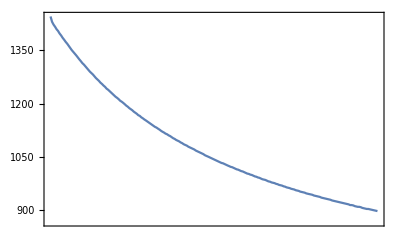

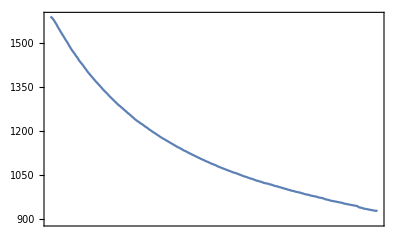

```mathematica
DateListPlot[rawdata[[1]]]
DateListPlot[rawdata[[2]]]
```

```mathematica
data = rawdata;
data[[1]] = TimeRefine[rawdata[[1]]];(*将时间换算为秒*)
data[[2]] = TimeRefine[rawdata[[2]]];
```

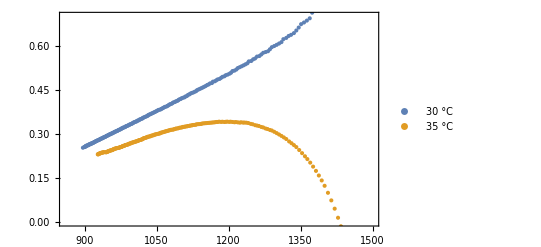

```mathematica
l0 = {data[[1,1,2]],data[[1,2,2]]};(*两组数据分别的初始电导率l0*)
linearfitdata = data;

linearfitdata[[1]] = Drop[LinearRefine[data[[1]],l0[[1]]],1];
linearfitdata[[2]] = Drop[LinearRefine[data[[2]],l0[[2]]],1];(*变换数据，变成线性*)

ListPlot[linearfitdata,PlotLegends->Placed[LineLegend[{"30 °C","35 °C"}, LegendFunction -> Frame], {0.85,0.75}],Frame->True,PlotRange->{{860,1500},{0,0.7}}]
```

可见并不是完全线性的，有一定的弯曲，可以发挥数理统计

```mathematica
framelabel = {"\!\(\*SubscriptBox[\(L\), \(t\)]\)","\!\(\*FractionBox[\(\*SubscriptBox[\(L\), \(0\)] - \*SubscriptBox[\(L\), \(t\)]\), \(t\)]\)"};
```

```mathematica
Export["/Users/royalty/Desktop/inone.jpg",ListPlot[linearfitdata,PlotLegends->Placed[LineLegend[{"30 °C","35 °C"}, LegendFunction -> Frame], {0.85,0.75}],Frame->True,PlotRange->{{860,1500},{0,0.7}}]]
```

/Users/royalty/Desktop/inone.jpg

### 丢弃数据，以相关系数大于 0.999 为标准

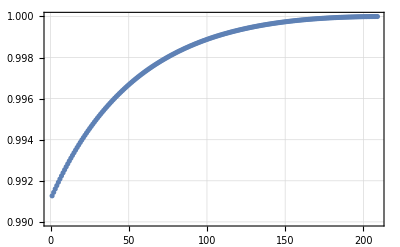

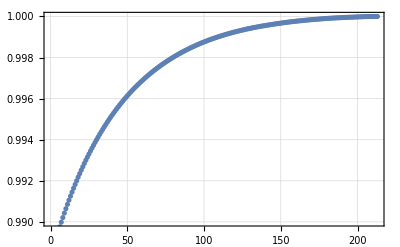

```mathematica
DropWisely[linearfitdata[[1]],t]
DropWisely[linearfitdata[[2]],t]
```

选择丢弃后面 150 个数据之后再进行线性拟合

```mathematica
linearmodel = LinearFitAll[{Drop[linearfitdata[[1]],150],Drop[linearfitdata[[2]],150]},t]
correlation = -{(linearmodel[[1]]["CorrelationMatrix"])[[1,2]],(linearmodel[[2]]["CorrelationMatrix"])[[1,2]]}
```

{FittedModel[-0.469706+0.000806369 t],FittedModel[-0.280937+0.000550699 t]}

{0.99974,0.999675}

```mathematica
linearmodel[[2]]["BestFitParameters"]
```

{-0.280937,0.000550699}

### 绘图

```mathematica
PlotRespectively=ListPlot[#1,Frame -> True, LabelStyle
     -> Directive[Black], GridLines -> Automatic, PlotLegends -> Placed[LineLegend[
    #2, LegendFunction -> Frame], #3],FrameLabel->#4, PlotStyle -> ColorData[
    #5, "ColorList"],PlotRange->#6]&;
```

```mathematica
todraw=Table[linearmodel[[i]][t],{i,1,2}]
```

{-0.469706+0.000806369 t,-0.280937+0.000550699 t}

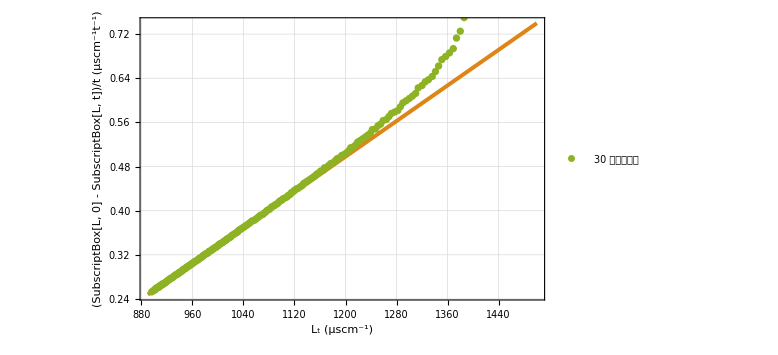

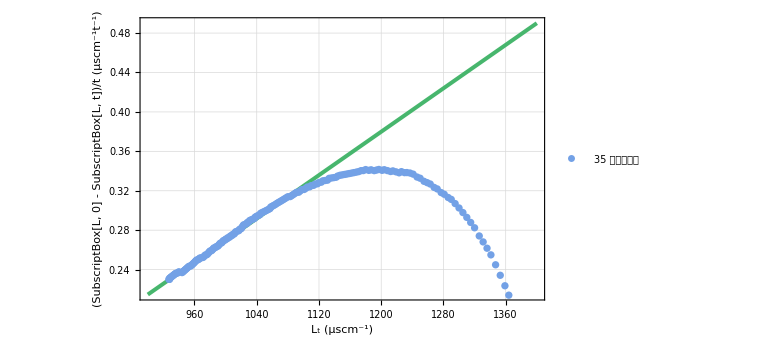

```mathematica
framelabel = {"\!\(\*SubscriptBox[\(L\), \(t\)]\) (μs\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\"·\", TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\cdot\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)\!\(\*SuperscriptBox[\(cm\), \(-1\)]\))","\!\(\*FractionBox[\((\*SubscriptBox[\(L\), \(0\)] - \*SubscriptBox[\(L\), \(t\)])\), \(t\)]\) (μs\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\"·\", TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\cdot\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)\!\(\*SuperscriptBox[\(cm\), \(-1\)]\)\!\(\*TemplateBox[<|\"boxes\" -> FormBox[\"·\", TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\cdot\", \"state\" -> \"Boxes\"|>,\n\"TeXAssistantTemplate\"]\)\!\(\*SuperscriptBox[\(t\), \(-1\)]\))"};

point1=PlotRespectively[linearfitdata[[1]],{"30 度实验结果"},{0.2,0.8},framelabel,78,Full];
point2=PlotRespectively[linearfitdata[[2]],{"35 度实验结果"},{0.2,0.8},framelabel,68,Full];

line1= Plot[todraw[[1]], {t, 890, 1500}, PlotRange
     -> Full, Frame -> True, LabelStyle -> Directive[Black], GridLines ->
     Automatic, PlotLegends -> Placed[LineLegend["xzcv", LegendFunction -> Frame
    ], {0.2,0.8}], FrameLabel -> framelabel, PlotStyle -> Directive[Thickness[0.005],ColorData[98,"ColorList"]], ImageSize -> Large];
line2= Plot[todraw[[2]], {t, 900, 1400}, PlotRange
     -> Full, Frame -> True, LabelStyle -> Directive[Black], GridLines ->
     Automatic, PlotLegends -> Placed[LineLegend["xzcv", LegendFunction -> Frame
    ], {0.2,0.8}], FrameLabel -> framelabel, PlotStyle -> Directive[Thickness[0.005],ColorData[97,"ColorList"]], ImageSize -> Large];
    
first=Show[line1,point1]
second=Show[line2,point2]
```

```mathematica
Export["/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp8/30degree.jpg",first]
Export["/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp8/35degree.jpg",second]
```

/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp8/30degree.jpg

/Users/royalty/Desktop/Experiments_for_Chemistry/physical_chemistry/Kecai_Xuan/exp8/35degree.jpg

```mathematica
{0.03,0.0254,0.0292,0.0277}/204.221
```

{0.0001469,0.000124375,0.000142982,0.000135637}

```mathematica
0.0001468996822070208/26.5*1000
0.00012437506426861094/22.9*1000
0.00014298235734816692/26.35*1000
0.00013563737323781587/25*1000
```

0.00554338

0.00543123

0.00542628

0.00542549

```mathematica
(5.42-5.43)/5.42
```

-0.00184502

```mathematica
8.06/5.42*0.1
```

0.148708

```mathematica
0.469/(8.06*10^-4)
```

581.886

## 数据表格输出

```mathematica
rawdata[[1,1]]
DateString/@rawdata[[1,1]]
```

```mathematica
out1=rawdata[[1]];
out2=rawdata[[2]];
Length[out1]
Length[out2]
```

```mathematica
For[i=1,i<=Length[out1],i++,
    out1[[i,1]]=DateString[rawdata[[1,i,1]]]
]
a=Take[out1,108];
b=Take[out1,-107];
Join[a,b,2]
Export["/Users/royalty/Desktop/dump.txt",%]
```

```mathematica
For[i=1,i<=Length[out2],i++,
    out2[[i,1]]=DateString[rawdata[[2,i,1]]]
]
a=Take[out2,110];
b=Take[out2,-109];
Join[a,b,2]
Export["/Users/royalty/Desktop/dump.txt",%]
```